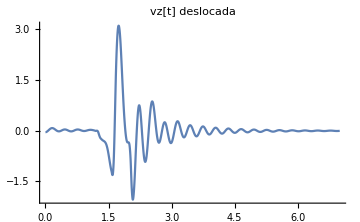
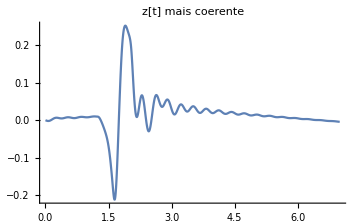

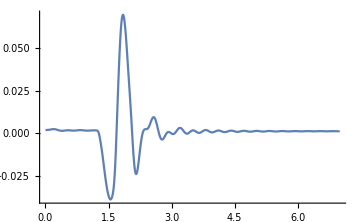
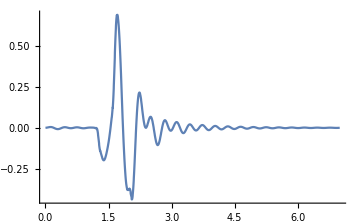

```mathematica
f=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\dataVz.txt"];
data1=ReadList[f,{Number,Number}];
Close[f];
a=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\data_Pitch_Angle.txt"];
data3=ReadList[a,{Number,Number}];
Close[a];
data2 =Subtract[data1,{{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490},{0,0.0490}}];


data4 = Times[data3, {{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)}}];

velocidade1= Interpolation[data1];
vz= Interpolation[data2];
u1[t] = Integrate[velocidade1[t],t];
z[t] =Integrate[vz[t],t];

angle1 = Interpolation[data3];
angle = Interpolation[data4];
omega = D[angle[t], t];
{

Plot[vz[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Medium, PlotLabel->"vz[t] deslocada"],
Plot[z[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Medium, PlotLabel->"z[t] mais coerente"]
}
{
Plot[angle[t],{t, 0, 7},PlotRange->{All, All}, ImageSize->Medium],
Plot[omega,{t, 0, 7},PlotRange->{All, All}, ImageSize->Medium]
}
```

```mathematica
xC1 = xot[t]+lot/2*Cos[θot[t]];
xB1 = xb[t]+ lb/2*Cos[θb[t]] + li*(Cos[θb[t]]*Cos[θ1[t]]-Sin[θb[t]]*Sin[θ1[t]]);
yC1 = yot[t] + lot/2*Sin[θot[t]];
yB1 = yb[t] + lb/2*Sin[θb[t]] + li*(Sin[θb[t]]*Cos[θ1[t]]+Sin[θ1[t]]*Cos[θb[t]]);
xC2 = xot[t]-lot/2*Cos[θot[t]];
xB2 =xb[t]- lb/2*Cos[θb[t]] + li*(Cos[θb[t]]*Cos[θ2[t]]-Sin[θb[t]]*Sin[θ2[t]]);
yC2 = yot[t] - lot/2*Sin[θot[t]];
yB2 = yb[t] - lb/2*Sin[θb[t]] + li*(Sin[θb[t]]*Cos[θ2[t]]+Cos[θb[t]]*Sin[θ2[t]]);

h1 = (xC1-xB1)^2+ (yC1 - yB1)^2 - ls^2 ;
h2 = (xC2 - xB2)^2+ (yC2 - yB2)^2 - ls^2 ;

h1expaux=Expand[h1];
h2expaux=Expand[h2];

h1dot = Expand[D[h1,t]];
h2dot = Expand[D[h2,t]];

h1dot2=Expand[D[h1,{t,2}]];
h2dot2 = Expand[D[h2,{t,2}]];

A = ({{D[h1dot,xot'[t]], D[h1dot,yot'[t]], D[h1dot,θot'[t]], D[h1dot,θ1'[t]], D[h1dot,θ2'[t]]}, {D[h2dot,xot'[t]], D[h2dot,yot'[t]], D[h2dot,θot'[t]], D[h2dot,θ1'[t]], D[h2dot,θ2'[t]]}});
MatrixForm[A];
At = Transpose[A];
MatrixForm[At];
λ=({{λ1[t]}, {λ2[t]}});
qdot = {{xot'[t],yot'[t],θot'[t],θ1'[t],θ2'[t]}};
qdot.At.λ;
```

```mathematica
(* Para o lado direito da maca θ1[t] *)
h1exp = -ls^2+1/4 lb^2 +lb li Cos[θ1[t]] Cos[θb[t]]^2+li^2 -1/2 lb lot Cos[θb[t]] Cos[θot[t]]-li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]]+1/4 lot^2+li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]]+lb li Cos[θ1[t]] Sin[θb[t]]^2-li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]]-1/2 lb lot Sin[θb[t]] Sin[θot[t]]-li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]]+lb Cos[θb[t]] xb[t]+2 li Cos[θ1[t]] Cos[θb[t]] xb[t]-lot Cos[θot[t]] xb[t]-2 li Sin[θ1[t]] Sin[θb[t]] xb[t]+xb[t]^2-lb Cos[θb[t]] xot[t]-2 li Cos[θ1[t]] Cos[θb[t]] xot[t]+lot Cos[θot[t]] xot[t]+2 li Sin[θ1[t]] Sin[θb[t]] xot[t]-2 xb[t] xot[t]+xot[t]^2+2 li Cos[θb[t]] Sin[θ1[t]] yb[t]+lb Sin[θb[t]] yb[t]+2 li Cos[θ1[t]] Sin[θb[t]] yb[t]-lot Sin[θot[t]] yb[t]+yb[t]^2-2 li Cos[θb[t]] Sin[θ1[t]] yot[t]-lb Sin[θb[t]] yot[t]-2 li Cos[θ1[t]] Sin[θb[t]] yot[t]+lot Sin[θot[t]] yot[t]-2 yb[t] yot[t]+yot[t]^2;
(* E1 Cos(θ1) + F1 Sin(θ1) + G1 = 0 *)

E1 = D[h1exp,Cos[θ1[t]]];
F1 =D[h1exp,Sin[θ1[t]]];
G1=Expand[h1exp]-Expand[E1*Cos[θ1[t]]]-Expand[F1*Sin[θ1[t]]];
u1 = (-F1+Sqrt[F1^2-G1^2+E1^2])/(G1-E1);
u2 = (-F1-Sqrt[F1^2-G1^2+E1^2])/(G1-E1);
theta11 = ArcCos[(1-u1^2)/(1+u1^2)]; (* configuração B1 posição interna *)
theta12 = ArcCos[(1-u2^2)/(1+u2^2)]; (* configuração B1 posição externa *)

Evaluate[theta11/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, xot[t]->0, yot[t]->0.342, xb[t]->0, yb[t]->0, θb[t]->0}];
Evaluate[theta12/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, xot[t]->0, yot[t]->0.38, xb[t]->0, yb[t]->0, θb[t]->0}]

(* Para o lado esquerdo da maca θ2[t] *)
h2exp = -ls^2+1/4 lb^2 -lb li Cos[θ2[t]] Cos[θb[t]]^2+li^2 -1/2 lb lot Cos[θb[t]] Cos[θot[t]]+li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]]+1/4 lot^2 -li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]]-lb li Cos[θ2[t]] Sin[θb[t]]^2+li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]]-1/2 lb lot Sin[θb[t]] Sin[θot[t]]+li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]]-lb Cos[θb[t]] xb[t]+2 li Cos[θ2[t]] Cos[θb[t]] xb[t]+lot Cos[θot[t]] xb[t]-2 li Sin[θ2[t]] Sin[θb[t]] xb[t]+xb[t]^2+lb Cos[θb[t]] xot[t]-2 li Cos[θ2[t]] Cos[θb[t]] xot[t]-lot Cos[θot[t]] xot[t]+2 li Sin[θ2[t]] Sin[θb[t]] xot[t]-2 xb[t] xot[t]+xot[t]^2+2 li Cos[θb[t]] Sin[θ2[t]] yb[t]-lb Sin[θb[t]] yb[t]+2 li Cos[θ2[t]] Sin[θb[t]] yb[t]+lot Sin[θot[t]] yb[t]+yb[t]^2-2 li Cos[θb[t]] Sin[θ2[t]] yot[t]+lb Sin[θb[t]] yot[t]-2 li Cos[θ2[t]] Sin[θb[t]] yot[t]-lot Sin[θot[t]] yot[t]-2 yb[t] yot[t]+yot[t]^2;
(* E2 Cos(θ2) + F2 Sin(θ2) + G2 = 0 *)

E2 = D[h2exp,Cos[θ2[t]]];
F2 =D[h2exp,Sin[θ2[t]]];
G2=Expand[h2exp]-Expand[E2*Cos[θ2[t]]]-Expand[F1*Sin[θ2[t]]];
v1 = (-F2+Sqrt[F2^2-G2^2+E2^2])/(G2-E2);
v2 = (-F2-Sqrt[F2^2-G2^2+E2^2])/(G2-E2);
theta21 = ArcCos[(1-v1^2)/(1+v1^2)]; (* configuração B2 posição externa *)
theta22 = ArcCos[(1-v2^2)/(1+v2^2)]; (* configuração B2 posição interna *)
Evaluate[theta21/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, xot[t]->0, yot[t]->0.38, xb[t]->0, yb[t]->0, θb[t]->0}]
Evaluate[theta22/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, xot[t]->0, yot[t]->0.342, xb[t]->0, yb[t]->0, θb[t]->0}];
```

0.983784

2.15781

```mathematica
T = 1/2 Mot ( D[xot[t],t]^2+D[yot[t],t]^2+ 1/12 lot^2 D[θot[t],t]^2);
V = Mot*g *yot[t]  + kb (xot[t]-xb[t])^2+ 1/2 kA (Pi/3-θ1[t])^2 + 1/2 kA (θ2[t]-(2*Pi)/3)^2;
R = cb (D[xot[t],t]-D[xb[t],t])^2+ 1/2 cA D[θ1[t],t]^2 + 1/2 cA D[θ2[t],t]^2;
P = qdot.At.λ;
H=P[[1]]//First;
```

```mathematica
𝕢[t_] = {xot[t],yot[t], θot[t], θ1[t], θ2[t]};
𝕖[t_] = Join[((D[D[T,D[#,t]],t]-D[T,#]+D[V,#]+D[R,D[#,t]]+D[H,D[#,t]]==0) & /@ 𝕢[t]),{(h1dot2==0) , (h2dot2 ==0)}];
𝕖[t]//TableForm
```

2 kb (-xb[t]+xot[t])+(-lb Cos[θb[t]]-2 li Cos[θ1[t]] Cos[θb[t]]+lot Cos[θot[t]]+2 li Sin[θ1[t]] Sin[θb[t]]-2 xb[t]+2 xot[t]) λ1[t]+(lb Cos[θb[t]]-2 li Cos[θ2[t]] Cos[θb[t]]-lot Cos[θot[t]]+2 li Sin[θ2[t]] Sin[θb[t]]-2 xb[t]+2 xot[t]) λ2[t]+2 cb (-xb'[t]+xot'[t])+Mot xot''[t]==0
g Mot+(-2 li Cos[θb[t]] Sin[θ1[t]]-lb Sin[θb[t]]-2 li Cos[θ1[t]] Sin[θb[t]]+lot Sin[θot[t]]-2 yb[t]+2 yot[t]) λ1[t]+(-2 li Cos[θb[t]] Sin[θ2[t]]+lb Sin[θb[t]]-2 li Cos[θ2[t]] Sin[θb[t]]-lot Sin[θot[t]]-2 yb[t]+2 yot[t]) λ2[t]+Mot yot''[t]==0
(-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]]-1/2 lb lot Cos[θot[t]] Sin[θb[t]]-li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]]+1/2 lb lot Cos[θb[t]] Sin[θot[t]]+li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]]-li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]]+lot Sin[θot[t]] xb[t]-lot Sin[θot[t]] xot[t]-lot Cos[θot[t]] yb[t]+lot Cos[θot[t]] yot[t]) λ1[t]+(li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]]-1/2 lb lot Cos[θot[t]] Sin[θb[t]]+li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]]+1/2 lb lot Cos[θb[t]] Sin[θot[t]]-li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]]+li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]]-lot Sin[θot[t]] xb[t]+lot Sin[θot[t]] xot[t]+lot Cos[θot[t]] yb[t]-lot Cos[θot[t]] yot[t]) λ2[t]+1/12 lot^2 Mot θot''[t]==0
-kA (π/3-θ1[t])+(-lb li Cos[θb[t]]^2 Sin[θ1[t]]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]]-lb li Sin[θ1[t]] Sin[θb[t]]^2-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]]-2 li Cos[θb[t]] Sin[θ1[t]] xb[t]-2 li Cos[θ1[t]] Sin[θb[t]] xb[t]+2 li Cos[θb[t]] Sin[θ1[t]] xot[t]+2 li Cos[θ1[t]] Sin[θb[t]] xot[t]+2 li Cos[θ1[t]] Cos[θb[t]] yb[t]-2 li Sin[θ1[t]] Sin[θb[t]] yb[t]-2 li Cos[θ1[t]] Cos[θb[t]] yot[t]+2 li Sin[θ1[t]] Sin[θb[t]] yot[t]) λ1[t]+cA θ1'[t]==0
kA (-(2 π)/3+θ2[t])+(lb li Cos[θb[t]]^2 Sin[θ2[t]]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]]+lb li Sin[θ2[t]] Sin[θb[t]]^2+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]]-2 li Cos[θb[t]] Sin[θ2[t]] xb[t]-2 li Cos[θ2[t]] Sin[θb[t]] xb[t]+2 li Cos[θb[t]] Sin[θ2[t]] xot[t]+2 li Cos[θ2[t]] Sin[θb[t]] xot[t]+2 li Cos[θ2[t]] Cos[θb[t]] yb[t]-2 li Sin[θ2[t]] Sin[θb[t]] yb[t]-2 li Cos[θ2[t]] Cos[θb[t]] yot[t]+2 li Sin[θ2[t]] Sin[θb[t]] yot[t]) λ2[t]+cA θ2'[t]==0
2 xb'[t]^2-4 xb'[t] xot'[t]+2 xot'[t]^2+2 yb'[t]^2-4 yb'[t] yot'[t]+2 yot'[t]^2-4 li Cos[θb[t]] Sin[θ1[t]] xb'[t] θ1'[t]-4 li Cos[θ1[t]] Sin[θb[t]] xb'[t] θ1'[t]+4 li Cos[θb[t]] Sin[θ1[t]] xot'[t] θ1'[t]+4 li Cos[θ1[t]] Sin[θb[t]] xot'[t] θ1'[t]+4 li Cos[θ1[t]] Cos[θb[t]] yb'[t] θ1'[t]-4 li Sin[θ1[t]] Sin[θb[t]] yb'[t] θ1'[t]-4 li Cos[θ1[t]] Cos[θb[t]] yot'[t] θ1'[t]+4 li Sin[θ1[t]] Sin[θb[t]] yot'[t] θ1'[t]-lb li Cos[θ1[t]] Cos[θb[t]]^2 θ1'[t]^2+li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θ1'[t]^2-li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θ1'[t]^2-lb li Cos[θ1[t]] Sin[θb[t]]^2 θ1'[t]^2+li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θ1'[t]^2+li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1'[t]^2-2 li Cos[θ1[t]] Cos[θb[t]] xb[t] θ1'[t]^2+2 li Sin[θ1[t]] Sin[θb[t]] xb[t] θ1'[t]^2+2 li Cos[θ1[t]] Cos[θb[t]] xot[t] θ1'[t]^2-2 li Sin[θ1[t]] Sin[θb[t]] xot[t] θ1'[t]^2-2 li Cos[θb[t]] Sin[θ1[t]] yb[t] θ1'[t]^2-2 li Cos[θ1[t]] Sin[θb[t]] yb[t] θ1'[t]^2+2 li Cos[θb[t]] Sin[θ1[t]] yot[t] θ1'[t]^2+2 li Cos[θ1[t]] Sin[θb[t]] yot[t] θ1'[t]^2-4 li Cos[θb[t]] Sin[θ1[t]] xb'[t] θb'[t]-2 lb Sin[θb[t]] xb'[t] θb'[t]-4 li Cos[θ1[t]] Sin[θb[t]] xb'[t] θb'[t]+4 li Cos[θb[t]] Sin[θ1[t]] xot'[t] θb'[t]+2 lb Sin[θb[t]] xot'[t] θb'[t]+4 li Cos[θ1[t]] Sin[θb[t]] xot'[t] θb'[t]+2 lb Cos[θb[t]] yb'[t] θb'[t]+4 li Cos[θ1[t]] Cos[θb[t]] yb'[t] θb'[t]-4 li Sin[θ1[t]] Sin[θb[t]] yb'[t] θb'[t]-2 lb Cos[θb[t]] yot'[t] θb'[t]-4 li Cos[θ1[t]] Cos[θb[t]] yot'[t] θb'[t]+4 li Sin[θ1[t]] Sin[θb[t]] yot'[t] θb'[t]+2 li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θ1'[t] θb'[t]-2 li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θ1'[t] θb'[t]+2 li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θ1'[t] θb'[t]+2 li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1'[t] θb'[t]-4 li Cos[θ1[t]] Cos[θb[t]] xb[t] θ1'[t] θb'[t]+4 li Sin[θ1[t]] Sin[θb[t]] xb[t] θ1'[t] θb'[t]+4 li Cos[θ1[t]] Cos[θb[t]] xot[t] θ1'[t] θb'[t]-4 li Sin[θ1[t]] Sin[θb[t]] xot[t] θ1'[t] θb'[t]-4 li Cos[θb[t]] Sin[θ1[t]] yb[t] θ1'[t] θb'[t]-4 li Cos[θ1[t]] Sin[θb[t]] yb[t] θ1'[t] θb'[t]+4 li Cos[θb[t]] Sin[θ1[t]] yot[t] θ1'[t] θb'[t]+4 li Cos[θ1[t]] Sin[θb[t]] yot[t] θ1'[t] θb'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θb'[t]^2+li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θb'[t]^2-li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θb'[t]^2+li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θb'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θb'[t]^2+li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θb'[t]^2-lb Cos[θb[t]] xb[t] θb'[t]^2-2 li Cos[θ1[t]] Cos[θb[t]] xb[t] θb'[t]^2+2 li Sin[θ1[t]] Sin[θb[t]] xb[t] θb'[t]^2+lb Cos[θb[t]] xot[t] θb'[t]^2+2 li Cos[θ1[t]] Cos[θb[t]] xot[t] θb'[t]^2-2 li Sin[θ1[t]] Sin[θb[t]] xot[t] θb'[t]^2-2 li Cos[θb[t]] Sin[θ1[t]] yb[t] θb'[t]^2-lb Sin[θb[t]] yb[t] θb'[t]^2-2 li Cos[θ1[t]] Sin[θb[t]] yb[t] θb'[t]^2+2 li Cos[θb[t]] Sin[θ1[t]] yot[t] θb'[t]^2+lb Sin[θb[t]] yot[t] θb'[t]^2+2 li Cos[θ1[t]] Sin[θb[t]] yot[t] θb'[t]^2+2 lot Sin[θot[t]] xb'[t] θot'[t]-2 lot Sin[θot[t]] xot'[t] θot'[t]-2 lot Cos[θot[t]] yb'[t] θot'[t]+2 lot Cos[θot[t]] yot'[t] θot'[t]-2 li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θ1'[t] θot'[t]+2 li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θ1'[t] θot'[t]-2 li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θ1'[t] θot'[t]-2 li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1'[t] θot'[t]-lb lot Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]-2 li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]+2 li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θb'[t] θot'[t]-2 li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θb'[t] θot'[t]-lb lot Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]-2 li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θot'[t]^2+li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θot'[t]^2-li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θot'[t]^2+li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θot'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θot'[t]^2+li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θot'[t]^2+lot Cos[θot[t]] xb[t] θot'[t]^2-lot Cos[θot[t]] xot[t] θot'[t]^2+lot Sin[θot[t]] yb[t] θot'[t]^2-lot Sin[θot[t]] yot[t] θot'[t]^2+lb Cos[θb[t]] xb''[t]+2 li Cos[θ1[t]] Cos[θb[t]] xb''[t]-lot Cos[θot[t]] xb''[t]-2 li Sin[θ1[t]] Sin[θb[t]] xb''[t]+2 xb[t] xb''[t]-2 xot[t] xb''[t]-lb Cos[θb[t]] xot''[t]-2 li Cos[θ1[t]] Cos[θb[t]] xot''[t]+lot Cos[θot[t]] xot''[t]+2 li Sin[θ1[t]] Sin[θb[t]] xot''[t]-2 xb[t] xot''[t]+2 xot[t] xot''[t]+2 li Cos[θb[t]] Sin[θ1[t]] yb''[t]+lb Sin[θb[t]] yb''[t]+2 li Cos[θ1[t]] Sin[θb[t]] yb''[t]-lot Sin[θot[t]] yb''[t]+2 yb[t] yb''[t]-2 yot[t] yb''[t]-2 li Cos[θb[t]] Sin[θ1[t]] yot''[t]-lb Sin[θb[t]] yot''[t]-2 li Cos[θ1[t]] Sin[θb[t]] yot''[t]+lot Sin[θot[t]] yot''[t]-2 yb[t] yot''[t]+2 yot[t] yot''[t]-lb li Cos[θb[t]]^2 Sin[θ1[t]] θ1''[t]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]] θ1''[t]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]] θ1''[t]-lb li Sin[θ1[t]] Sin[θb[t]]^2 θ1''[t]-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]] θ1''[t]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1''[t]-2 li Cos[θb[t]] Sin[θ1[t]] xb[t] θ1''[t]-2 li Cos[θ1[t]] Sin[θb[t]] xb[t] θ1''[t]+2 li Cos[θb[t]] Sin[θ1[t]] xot[t] θ1''[t]+2 li Cos[θ1[t]] Sin[θb[t]] xot[t] θ1''[t]+2 li Cos[θ1[t]] Cos[θb[t]] yb[t] θ1''[t]-2 li Sin[θ1[t]] Sin[θb[t]] yb[t] θ1''[t]-2 li Cos[θ1[t]] Cos[θb[t]] yot[t] θ1''[t]+2 li Sin[θ1[t]] Sin[θb[t]] yot[t] θ1''[t]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]] θb''[t]+1/2 lb lot Cos[θot[t]] Sin[θb[t]] θb''[t]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]] θb''[t]-1/2 lb lot Cos[θb[t]] Sin[θot[t]] θb''[t]-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]] θb''[t]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]] θb''[t]-2 li Cos[θb[t]] Sin[θ1[t]] xb[t] θb''[t]-lb Sin[θb[t]] xb[t] θb''[t]-2 li Cos[θ1[t]] Sin[θb[t]] xb[t] θb''[t]+2 li Cos[θb[t]] Sin[θ1[t]] xot[t] θb''[t]+lb Sin[θb[t]] xot[t] θb''[t]+2 li Cos[θ1[t]] Sin[θb[t]] xot[t] θb''[t]+lb Cos[θb[t]] yb[t] θb''[t]+2 li Cos[θ1[t]] Cos[θb[t]] yb[t] θb''[t]-2 li Sin[θ1[t]] Sin[θb[t]] yb[t] θb''[t]-lb Cos[θb[t]] yot[t] θb''[t]-2 li Cos[θ1[t]] Cos[θb[t]] yot[t] θb''[t]+2 li Sin[θ1[t]] Sin[θb[t]] yot[t] θb''[t]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]] θot''[t]-1/2 lb lot Cos[θot[t]] Sin[θb[t]] θot''[t]-li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]] θot''[t]+1/2 lb lot Cos[θb[t]] Sin[θot[t]] θot''[t]+li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]] θot''[t]-li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]] θot''[t]+lot Sin[θot[t]] xb[t] θot''[t]-lot Sin[θot[t]] xot[t] θot''[t]-lot Cos[θot[t]] yb[t] θot''[t]+lot Cos[θot[t]] yot[t] θot''[t]==0
2 xb'[t]^2-4 xb'[t] xot'[t]+2 xot'[t]^2+2 yb'[t]^2-4 yb'[t] yot'[t]+2 yot'[t]^2-4 li Cos[θb[t]] Sin[θ2[t]] xb'[t] θ2'[t]-4 li Cos[θ2[t]] Sin[θb[t]] xb'[t] θ2'[t]+4 li Cos[θb[t]] Sin[θ2[t]] xot'[t] θ2'[t]+4 li Cos[θ2[t]] Sin[θb[t]] xot'[t] θ2'[t]+4 li Cos[θ2[t]] Cos[θb[t]] yb'[t] θ2'[t]-4 li Sin[θ2[t]] Sin[θb[t]] yb'[t] θ2'[t]-4 li Cos[θ2[t]] Cos[θb[t]] yot'[t] θ2'[t]+4 li Sin[θ2[t]] Sin[θb[t]] yot'[t] θ2'[t]+lb li Cos[θ2[t]] Cos[θb[t]]^2 θ2'[t]^2-li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θ2'[t]^2+li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θ2'[t]^2+lb li Cos[θ2[t]] Sin[θb[t]]^2 θ2'[t]^2-li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θ2'[t]^2-li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2'[t]^2-2 li Cos[θ2[t]] Cos[θb[t]] xb[t] θ2'[t]^2+2 li Sin[θ2[t]] Sin[θb[t]] xb[t] θ2'[t]^2+2 li Cos[θ2[t]] Cos[θb[t]] xot[t] θ2'[t]^2-2 li Sin[θ2[t]] Sin[θb[t]] xot[t] θ2'[t]^2-2 li Cos[θb[t]] Sin[θ2[t]] yb[t] θ2'[t]^2-2 li Cos[θ2[t]] Sin[θb[t]] yb[t] θ2'[t]^2+2 li Cos[θb[t]] Sin[θ2[t]] yot[t] θ2'[t]^2+2 li Cos[θ2[t]] Sin[θb[t]] yot[t] θ2'[t]^2-4 li Cos[θb[t]] Sin[θ2[t]] xb'[t] θb'[t]+2 lb Sin[θb[t]] xb'[t] θb'[t]-4 li Cos[θ2[t]] Sin[θb[t]] xb'[t] θb'[t]+4 li Cos[θb[t]] Sin[θ2[t]] xot'[t] θb'[t]-2 lb Sin[θb[t]] xot'[t] θb'[t]+4 li Cos[θ2[t]] Sin[θb[t]] xot'[t] θb'[t]-2 lb Cos[θb[t]] yb'[t] θb'[t]+4 li Cos[θ2[t]] Cos[θb[t]] yb'[t] θb'[t]-4 li Sin[θ2[t]] Sin[θb[t]] yb'[t] θb'[t]+2 lb Cos[θb[t]] yot'[t] θb'[t]-4 li Cos[θ2[t]] Cos[θb[t]] yot'[t] θb'[t]+4 li Sin[θ2[t]] Sin[θb[t]] yot'[t] θb'[t]-2 li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θ2'[t] θb'[t]+2 li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θ2'[t] θb'[t]-2 li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θ2'[t] θb'[t]-2 li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2'[t] θb'[t]-4 li Cos[θ2[t]] Cos[θb[t]] xb[t] θ2'[t] θb'[t]+4 li Sin[θ2[t]] Sin[θb[t]] xb[t] θ2'[t] θb'[t]+4 li Cos[θ2[t]] Cos[θb[t]] xot[t] θ2'[t] θb'[t]-4 li Sin[θ2[t]] Sin[θb[t]] xot[t] θ2'[t] θb'[t]-4 li Cos[θb[t]] Sin[θ2[t]] yb[t] θ2'[t] θb'[t]-4 li Cos[θ2[t]] Sin[θb[t]] yb[t] θ2'[t] θb'[t]+4 li Cos[θb[t]] Sin[θ2[t]] yot[t] θ2'[t] θb'[t]+4 li Cos[θ2[t]] Sin[θb[t]] yot[t] θ2'[t] θb'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θb'[t]^2-li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θb'[t]^2+li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θb'[t]^2-li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θb'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θb'[t]^2-li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θb'[t]^2+lb Cos[θb[t]] xb[t] θb'[t]^2-2 li Cos[θ2[t]] Cos[θb[t]] xb[t] θb'[t]^2+2 li Sin[θ2[t]] Sin[θb[t]] xb[t] θb'[t]^2-lb Cos[θb[t]] xot[t] θb'[t]^2+2 li Cos[θ2[t]] Cos[θb[t]] xot[t] θb'[t]^2-2 li Sin[θ2[t]] Sin[θb[t]] xot[t] θb'[t]^2-2 li Cos[θb[t]] Sin[θ2[t]] yb[t] θb'[t]^2+lb Sin[θb[t]] yb[t] θb'[t]^2-2 li Cos[θ2[t]] Sin[θb[t]] yb[t] θb'[t]^2+2 li Cos[θb[t]] Sin[θ2[t]] yot[t] θb'[t]^2-lb Sin[θb[t]] yot[t] θb'[t]^2+2 li Cos[θ2[t]] Sin[θb[t]] yot[t] θb'[t]^2-2 lot Sin[θot[t]] xb'[t] θot'[t]+2 lot Sin[θot[t]] xot'[t] θot'[t]+2 lot Cos[θot[t]] yb'[t] θot'[t]-2 lot Cos[θot[t]] yot'[t] θot'[t]+2 li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θ2'[t] θot'[t]-2 li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θ2'[t] θot'[t]+2 li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θ2'[t] θot'[t]+2 li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2'[t] θot'[t]-lb lot Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]+2 li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]-2 li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θb'[t] θot'[t]+2 li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θb'[t] θot'[t]-lb lot Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]+2 li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θot'[t]^2-li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θot'[t]^2+li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θot'[t]^2-li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θot'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θot'[t]^2-li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θot'[t]^2-lot Cos[θot[t]] xb[t] θot'[t]^2+lot Cos[θot[t]] xot[t] θot'[t]^2-lot Sin[θot[t]] yb[t] θot'[t]^2+lot Sin[θot[t]] yot[t] θot'[t]^2-lb Cos[θb[t]] xb''[t]+2 li Cos[θ2[t]] Cos[θb[t]] xb''[t]+lot Cos[θot[t]] xb''[t]-2 li Sin[θ2[t]] Sin[θb[t]] xb''[t]+2 xb[t] xb''[t]-2 xot[t] xb''[t]+lb Cos[θb[t]] xot''[t]-2 li Cos[θ2[t]] Cos[θb[t]] xot''[t]-lot Cos[θot[t]] xot''[t]+2 li Sin[θ2[t]] Sin[θb[t]] xot''[t]-2 xb[t] xot''[t]+2 xot[t] xot''[t]+2 li Cos[θb[t]] Sin[θ2[t]] yb''[t]-lb Sin[θb[t]] yb''[t]+2 li Cos[θ2[t]] Sin[θb[t]] yb''[t]+lot Sin[θot[t]] yb''[t]+2 yb[t] yb''[t]-2 yot[t] yb''[t]-2 li Cos[θb[t]] Sin[θ2[t]] yot''[t]+lb Sin[θb[t]] yot''[t]-2 li Cos[θ2[t]] Sin[θb[t]] yot''[t]-lot Sin[θot[t]] yot''[t]-2 yb[t] yot''[t]+2 yot[t] yot''[t]+lb li Cos[θb[t]]^2 Sin[θ2[t]] θ2''[t]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]] θ2''[t]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]] θ2''[t]+lb li Sin[θ2[t]] Sin[θb[t]]^2 θ2''[t]+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]] θ2''[t]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2''[t]-2 li Cos[θb[t]] Sin[θ2[t]] xb[t] θ2''[t]-2 li Cos[θ2[t]] Sin[θb[t]] xb[t] θ2''[t]+2 li Cos[θb[t]] Sin[θ2[t]] xot[t] θ2''[t]+2 li Cos[θ2[t]] Sin[θb[t]] xot[t] θ2''[t]+2 li Cos[θ2[t]] Cos[θb[t]] yb[t] θ2''[t]-2 li Sin[θ2[t]] Sin[θb[t]] yb[t] θ2''[t]-2 li Cos[θ2[t]] Cos[θb[t]] yot[t] θ2''[t]+2 li Sin[θ2[t]] Sin[θb[t]] yot[t] θ2''[t]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]] θb''[t]+1/2 lb lot Cos[θot[t]] Sin[θb[t]] θb''[t]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]] θb''[t]-1/2 lb lot Cos[θb[t]] Sin[θot[t]] θb''[t]+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]] θb''[t]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]] θb''[t]-2 li Cos[θb[t]] Sin[θ2[t]] xb[t] θb''[t]+lb Sin[θb[t]] xb[t] θb''[t]-2 li Cos[θ2[t]] Sin[θb[t]] xb[t] θb''[t]+2 li Cos[θb[t]] Sin[θ2[t]] xot[t] θb''[t]-lb Sin[θb[t]] xot[t] θb''[t]+2 li Cos[θ2[t]] Sin[θb[t]] xot[t] θb''[t]-lb Cos[θb[t]] yb[t] θb''[t]+2 li Cos[θ2[t]] Cos[θb[t]] yb[t] θb''[t]-2 li Sin[θ2[t]] Sin[θb[t]] yb[t] θb''[t]+lb Cos[θb[t]] yot[t] θb''[t]-2 li Cos[θ2[t]] Cos[θb[t]] yot[t] θb''[t]+2 li Sin[θ2[t]] Sin[θb[t]] yot[t] θb''[t]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]] θot''[t]-1/2 lb lot Cos[θot[t]] Sin[θb[t]] θot''[t]+li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]] θot''[t]+1/2 lb lot Cos[θb[t]] Sin[θot[t]] θot''[t]-li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]] θot''[t]+li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]] θot''[t]-lot Sin[θot[t]] xb[t] θot''[t]+lot Sin[θot[t]] xot[t] θot''[t]+lot Cos[θot[t]] yb[t] θot''[t]-lot Cos[θot[t]] yot[t] θot''[t]==0

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

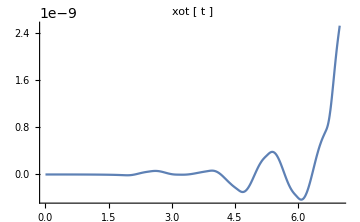
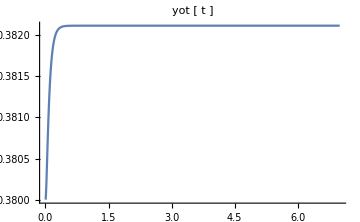
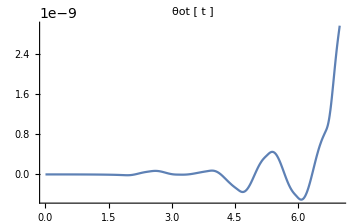
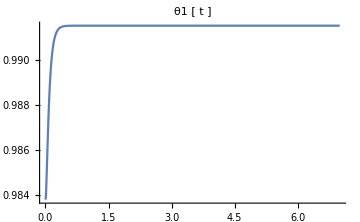
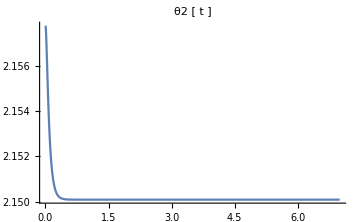
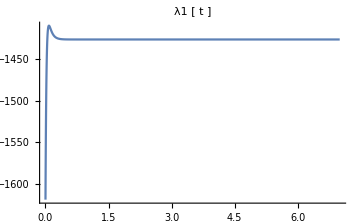
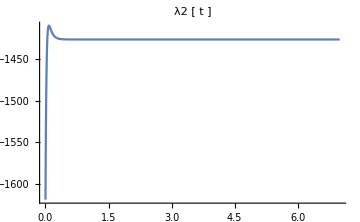
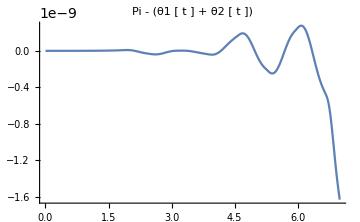

```mathematica
eqs=(𝕖[t]/.{Mot->125,g->9.8,lot->1.8, lb->2, li -> 0.2, ls-> 0.3, kA->3000,cA->266, kb->5600,cb->266,xb[t_]->0, xb'[t_]->0, xb''[t_]->0,yb[t_]->0, yb'[t_]->0, yb''[t_]->0, θb[t_]->0, θb'[t_]->0, θb''[t_]->0})/.Rule->Equal;
Module[{sol, ti=0, ts=7}, sol= NDSolve[Join[eqs, {xot[0]==0,yot[0]==0.38,θot[0]==0,θ1[0]==0.9837836701010994, θ2[0]==2.1578089834886907,yot'[0]==0, xot'[0]==0,θot'[0]==0, θ1'[0]==0, θ2'[0]==0}],{xot,yot,θot,θ1,θ2, λ1,λ2},{t,0,ts}];
{Plot[ Evaluate[(xot[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"xot [ t ]"],
Plot[ Evaluate[(yot[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"yot [ t ]"],
Plot[ Evaluate[(θot[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"θot [ t ]"],
Plot[ Evaluate[(θ1[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"θ1 [ t ]"],
Plot[ Evaluate[(θ2[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"θ2 [ t ]"],
Plot[ Evaluate[(λ1[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"λ1 [ t ]"],
Plot[ Evaluate[(λ2[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"λ2 [ t ]"],
Plot[ Evaluate[(Pi-(θ1[t]+θ2[t])/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Medium, LabelStyle->"Subsubsection", PlotLabel->"Pi - (θ1 [ t ] + θ2 [ t ])"]}
]
```